```mathematica
(* visualise phylogenies and recombination gene presence/absence *)
(* there is no analysis here -- just visualisation. this pipeline is messy and we aim to smoothen it with ETE3 or phytools in future! *)
```

```mathematica
(* read presence/absence barcodes *)
```

```mathematica
SetDirectory["~/Dropbox/EvoConBiO/WP3/Curate/Phylogenetics/"]
```

/home/iain/Dropbox/EvoConBiO/WP3/Curate/Phylogenetics

```mathematica
barcodes = ReadList["barcodes.txt", String];
```

```mathematica
(* read nodes and edges *)
```

```mathematica
l = ReadList["commontree.txt-old.txt.padded-edges", {Number, Number}];
s = ReadList["commontree.txt-old.txt.padded-labels", String];
```

```mathematica
(* build graph and labels *)
```

```mathematica
g = {};
For[i=1,i≤Length[l],i++,
AppendTo[g, l[[i]][[1]]->l[[i]][[2]]];
];
```

```mathematica
blabels= bcodes = {};
For[i=2,i≤Length[barcodes],i++,
tmp = StringSplit[barcodes[[i]], " "];
AppendTo[blabels,StringSplit[tmp[[2]], "\""][[1]]<>" "<>StringSplit[tmp[[3]], "\""][[1]]];
AppendTo[bcodes, {ToExpression[tmp[[4]]], ToExpression[tmp[[5]]], ToExpression[tmp[[6]]], ToExpression[tmp[[7]]]}];
];
```

```mathematica
notables = {"Eukaryota","Fungi", "Viridiplantae", "Metazoa", "Anthozoa", "Placozoa", "Apicomplexa", "Chordata", "Magnoliopsida", "Arthropoda", "Porifera"}
```

{Eukaryota,Fungi,Viridiplantae,Metazoa,Anthozoa,Placozoa,Apicomplexa,Chordata,Magnoliopsida,Arthropoda,Porifera}

```mathematica
offset[str_]:= If[str=="Porifera", {-0.2,0}, {0,0}]
```

```mathematica
vfn[vlabel_, vpos_]:= {If[Length[Position[notables, s[[vlabel]]]] ≠ 0, Style[Text[s[[vlabel]], vpos+offset[s[[vlabel]]], {-1,0},{0,1}], 12]],If[Length[Position[blabels, s[[vlabel]]]] ≠ 0, Table[If[bcodes[[Position[blabels, s[[vlabel]]][[1]][[1]]]][[i]]==1,{Black, Rectangle[vpos+{0,-0.05-0.025*i},vpos+{0,-0.05-0.025*i}+{0.05,0.02}]}], {i, 1, 4}]]};
```

Part::partw: Part 2485 of {Eukaryota,Rotosphaerida,ghost,ghost,ghost,ghost,ghost,Fonticula alba,Apusomonadidae,ghost,ghost,ghost,ghost,ghost,Thecamonas trahens,Cercozoa,ghost1,ghost1,ghost1,ghost1,ghost1,Bigelowiella natans,Filasterea,ghost1,ghost1,ghost1,ghost1,ghost1,Capsaspora owczarzaki,Choanoflagellata,Salpingoecidae,Salpingoeca,ghost2,ghost2,ghost2,Salpingoeca rosetta,Monosiga,ghost2,ghost2,ghost2,Monosiga brevicollis,Eustigmatophyceae,ghost2,ghost2,ghost2,ghost2,ghost3,Nannochloropsis gaditana,Ichthyosporea,ghost3,«2434»} does not exist.

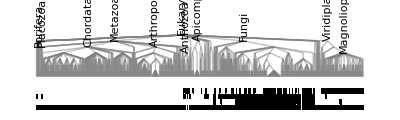

```mathematica
TreePlot[g, VertexRenderingFunction->(vfn[#2, #1]&), EdgeRenderingFunction->({Opacity[0.5], Gray,Line[#]}&), AspectRatio->0.3]
```

```mathematica
set = {1};
subg = {};
For[level = 1, level ≤ 3, level++,
nset = {};
For[j=1,j≤ Length[g],j++,
r = g[[j]][[1]];
If[Length[Position[set,r]]≠ 0,
AppendTo[nset, g[[j]][[2]]];
AppendTo[subg, g[[j]]];
];
];
set = Union[set, nset];
];
```

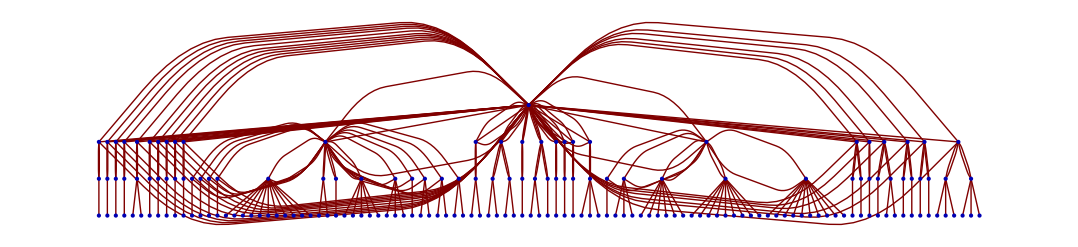

```mathematica
TreePlot[subg]
```

```mathematica
set = {1};
subg = bottomset = {};
For[level = 1, level ≤ 2, level++,
nset = {};
For[j=1,j≤ Length[g],j++,
r = g[[j]][[1]];
If[Length[Position[set,r]]≠ 0,
AppendTo[nset, g[[j]][[2]]];
If[level == 2,
Print[g[[j]]];
AppendTo[bottomset, g[[j]][[2]]];
];
AppendTo[subg, g[[j]]];
];
];
set = Union[set, nset];
];
subg = Union[subg];
```

```mathematica
am = Table[{g[[i]][[1]], g[[i]][[2]]}, {i, 1, Length[g]}];
```

```mathematica
n = Max[Transpose[am][[2]]]
```

2485

```mathematica
meanbcodes = Table[{0,0,0,0}, {i, 1, n}];
nbcodes = Table[0, {i, 1, n}];
For[i=1,i≤n,i++,
If[Length[Position[blabels, s[[i]]]] ≠ 0,
For[current = i,1 > 0,
ref = Position[Transpose[am][[2]], current];
If[Length[ref] == 0 || Position[bottomset,current] ≠ {}, parent = current; Break[]];
ref = ref[[1]][[1]];
current = am[[ref]][[1]];
];
meanbcodes[[parent]] += bcodes[[Position[blabels, s[[i]]][[1]][[1]]]];
nbcodes[[parent]]++;
];
];
```

Part::partw: Part 2485 of {Eukaryota,Rotosphaerida,ghost,ghost,ghost,ghost,ghost,Fonticula alba,Apusomonadidae,ghost,ghost,ghost,ghost,ghost,Thecamonas trahens,Cercozoa,ghost1,ghost1,ghost1,ghost1,ghost1,Bigelowiella natans,Filasterea,ghost1,ghost1,ghost1,ghost1,ghost1,Capsaspora owczarzaki,Choanoflagellata,Salpingoecidae,Salpingoeca,ghost2,ghost2,ghost2,Salpingoeca rosetta,Monosiga,ghost2,ghost2,ghost2,Monosiga brevicollis,Eustigmatophyceae,ghost2,ghost2,ghost2,ghost2,ghost3,Nannochloropsis gaditana,Ichthyosporea,ghost3,«2434»} does not exist.

```mathematica
bottomset
```

{2,3,9,10,16,17,23,24,30,31,42,43,49,50,56,57,64,65,71,72,79,80,86,92,98,104,855,866,872,1151,1184,1190,1215,1230,1282,1283,1298,1299,1336,1368,1369,1375,1376,1395,1404,1405,1411,1412,1418,1419,1425,1426,1452,1453,1463,1479,1513,1670,2103,2104,2116,2128,2129,2135,2136,2142,2153,2154,2160,2166,2167,2177,2183,2184,2220}

```mathematica
nbcodes[[bottomset]]
```

{0,1,0,1,0,1,0,1,0,2,0,1,0,1,0,2,0,1,0,2,0,1,1,1,1,258,2,1,118,8,1,8,3,18,0,3,0,25,13,0,1,0,3,4,0,1,0,0,0,1,0,13,0,2,3,9,45,208,0,4,4,0,1,0,1,2,0,1,1,0,2,1,0,10,111}

```mathematica
subvfn[vlabel_, vpos_]:= {If[!StringContainsQ[s[[vlabel]], "ghost"], {Style[Text[s[[vlabel]], vpos+offset[s[[vlabel]]], {-1,0},{0,1}], 12]}]}
```

```mathematica
newbcodefn[vlabel_, vpos_]:={If[Length[Position[bottomset, vlabel]] ≠ 0, Table[{GrayLevel[1-meanbcodes[[vlabel]][[i]]/nbcodes[[vlabel]][[i]]], Rectangle[vpos+{0,-0.05-0.025*i},vpos+{0,-0.05-0.025*i}+{0.05,0.02}]}, {i, 1, 4}]]};
```

```mathematica
TreePlot[subg, VertexRenderingFunction->({subvfn[#2, #1], newbcodefn[#2,#1]}&), EdgeRenderingFunction->({Opacity[0.5], Gray,Line[#]}&), AspectRatio->0.3]
```

Part::partd: Part specification 0⟦1⟧ is longer than depth of object.

Part::partd: Part specification 0⟦2⟧ is longer than depth of object.

Part::partd: Part specification 0⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

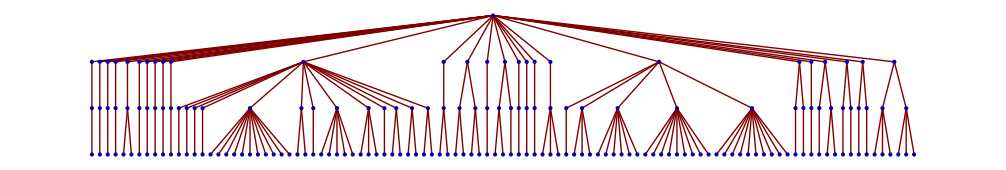

```mathematica
TreePlot[subg]
```

```mathematica
(* the code below does the same thing for individual genes, and other subsets of interest *)
```

```mathematica
l = ReadList["msh1-blastx-tree.txt-old.txt.padded-edges", {Number, Number}];
s = ReadList["msh1-blastx-tree.txt-old.txt.padded-labels", String];
```

```mathematica
g = {};
For[i=1,i≤Length[l],i++,
AppendTo[g, l[[i]][[1]]->l[[i]][[2]]];
];
```

```mathematica
notables = {"Eukaryota","Fungi", "Viridiplantae",  "Anthozoa", "Placozoa", "Porifera","Apicomplexa", "Chordata", "Magnoliopsida", "Arthropoda", "Hexacorallia","Actiniaria","Antipatharia","Corallimorpharia","Scleractinia","Zoantharia","Octocorallia","Alcyonacea","Helioporacea","Pennatulacea","Ceriantharia","Penicillaria","Spirularia", "Porifera", "Actiniaria", "Basidiomycota", "Ascomycota"}
```

{Eukaryota,Fungi,Viridiplantae,Anthozoa,Placozoa,Porifera,Apicomplexa,Chordata,Magnoliopsida,Arthropoda,Hexacorallia,Actiniaria,Antipatharia,Corallimorpharia,Scleractinia,Zoantharia,Octocorallia,Alcyonacea,Helioporacea,Pennatulacea,Ceriantharia,Penicillaria,Spirularia,Porifera,Actiniaria,Basidiomycota,Ascomycota}

```mathematica
offset[str_]:= If[str=="Fungi", {-0.2,0}, {0,0}]
```

```mathematica
vfn[vlabel_, vpos_]:= {If[Length[Position[notables, s[[vlabel]]]] ≠ 0, Text[s[[vlabel]], vpos+offset[s[[vlabel]]], {-1,0},{0,1}]]};
```

Part::partw: Part 7299 of {Rhodopseudomonas palustris BisB5,-----------------------------------,Eukaryota,Bigyra,ghost,ghost,ghost,ghost,ghost,ghost,Hondaea fermentalgiana,Vitrellaceae,ghost,ghost,ghost,ghost,ghost1,ghost1,Vitrella brassicaformis CCMP3155,Cryptophyceae,ghost1,ghost1,ghost1,ghost1,ghost1,ghost1,Guillardia theta CCMP2712,Ichthyosporea,ghost1,ghost1,ghost2,ghost2,ghost2,ghost2,Sphaeroforma arctica JP610,Apicomplexa,ghost2,ghost2,ghost2,ghost2,ghost2,ghost2,Cardiosporidium cionae,Apusomonadidae,ghost3,ghost3,ghost3,ghost3,ghost3,ghost3,«7248»} does not exist.

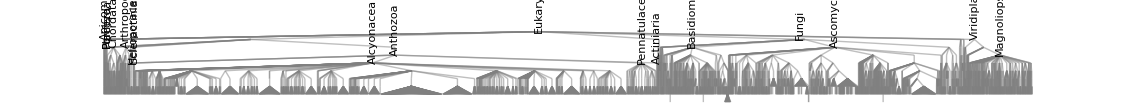

```mathematica
TreePlot[g, VertexRenderingFunction->(vfn[#2, #1]&), EdgeRenderingFunction->({Opacity[0.5], Gray,Line[#]}&), AspectRatio->0.1]
```

```mathematica
l = ReadList["mgm101-blastx-tree.txt-old.txt.padded-edges", {Number, Number}];
s = ReadList["mgm101-blastx-tree.txt-old.txt.padded-labels", String];
```

```mathematica
g = {};
For[i=1,i≤Length[l],i++,
AppendTo[g, l[[i]][[1]]->l[[i]][[2]]];
];
```

```mathematica
notables = {"Eukaryota","Fungi", "Viridiplantae",  "Anthozoa", "Placozoa", "Apicomplexa", "Chordata", "Magnoliopsida", "Arthropoda", "Porifera", "Ascomycota", "Basidiomycota", "Dictyosteliales" , "Physariida", "Mucoromycota", "Dothideomycetes","Eurotiomycetes", "Sordariomycetes", "Saccharomycetes", "Agaricomycetes" , "Microbotryomycetes", "Tremellomycetes", "Actiniaria"}
```

{Eukaryota,Fungi,Viridiplantae,Anthozoa,Placozoa,Apicomplexa,Chordata,Magnoliopsida,Arthropoda,Porifera,Ascomycota,Basidiomycota,Dictyosteliales,Physariida,Mucoromycota,Dothideomycetes,Eurotiomycetes,Sordariomycetes,Saccharomycetes,Agaricomycetes,Microbotryomycetes,Tremellomycetes,Actiniaria}

```mathematica
yoff = 0.1;
```

```mathematica
offset[str_]:= If[str=="Viridiplantae", {-0.1,yoff},If[str=="Porifera", {-0.1,0},If[str=="Placozoa", {0.,yoff},If[str=="Physariida", {0.25,yoff}, If[str=="Actiniaria", {0.1,yoff},If[str=="Dictyosteliales", {0.35,0},If[str=="Basidiomycota", {0.25,0},{0,0}]]]]] ]]
```

```mathematica
vfn[vlabel_, vpos_]:= {If[Length[Position[notables, s[[vlabel]]]] ≠ 0, Text[s[[vlabel]], vpos+offset[s[[vlabel]]], {-1,0},{0,1}]]};
```

Part::partw: Part 3856 of {Eukaryota,Discosea,ghost,ghost,ghost,ghost,ghost,ghost,ghost,Acanthamoeba castellanii str. Neff,Rotosphaerida,ghost,ghost,ghost,ghost1,ghost1,ghost1,ghost1,Fonticula alba,Jakobida,ghost1,ghost1,ghost1,ghost1,ghost1,ghost1,ghost2,Andalucia godoyi,Viridiplantae,Fagales,Betulaceae,ghost2,ghost2,ghost2,ghost2,ghost2,Carpinus fangiana,Fagaceae,ghost2,ghost2,ghost2,ghost2,ghost3,Quercus suber,Metazoa,Porifera,ghost3,ghost3,ghost3,ghost3,«3805»} does not exist.

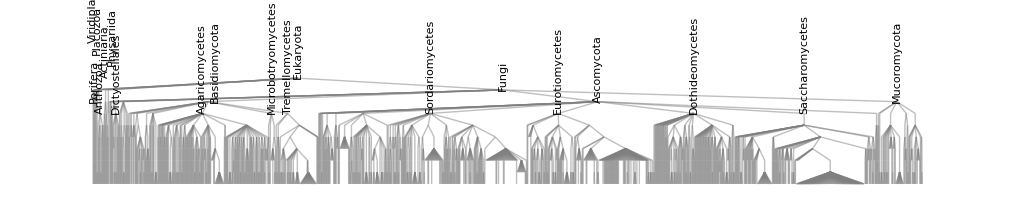

```mathematica
TreePlot[g, VertexRenderingFunction->(vfn[#2, #1]&), EdgeRenderingFunction->({Opacity[0.5], Gray,Line[#]}&), AspectRatio->0.2]
```

```mathematica
l = ReadList["mhr1-blastx-tree.txt-old.txt.padded-edges", {Number, Number}];
s = ReadList["mhr1-blastx-tree.txt-old.txt.padded-labels", String];
```

```mathematica
g = {};
For[i=1,i≤Length[l],i++,
AppendTo[g, l[[i]][[1]]->l[[i]][[2]]];
];
```

```mathematica
notables = {"Eukaryota","Fungi", "Viridiplantae",  "Anthozoa", "Placozoa", "Apicomplexa", "Chordata", "Magnoliopsida", "Arthropoda", "Porifera", "Ascomycota", "Basidiomycota",  "Basidiomycota", "Dictyosteliales" , "Physariida", "Mucoromycota", "Dothideomycetes","Eurotiomycetes", "Sordariomycetes", "Saccharomycetes", "Agaricomycetes" , "Microbotryomycetes", "Tremellomycetes"}
```

{Eukaryota,Fungi,Viridiplantae,Anthozoa,Placozoa,Apicomplexa,Chordata,Magnoliopsida,Arthropoda,Porifera,Ascomycota,Basidiomycota,Basidiomycota,Dictyosteliales,Physariida,Mucoromycota,Dothideomycetes,Eurotiomycetes,Sordariomycetes,Saccharomycetes,Agaricomycetes,Microbotryomycetes,Tremellomycetes}

```mathematica
vfn[vlabel_, vpos_]:= {If[Length[Position[notables, s[[vlabel]]]] ≠ 0, Text[s[[vlabel]], vpos, {-1,0},{0,1}]]};
```

Part::partw: Part 482 of {Fungi,Mucoromycota,ghost,ghost,ghost,ghost,ghost,ghost,Mucor plumbeus,Ascomycota,Dothideomycetes,Zopfiaceae,ghost,ghost,ghost,ghost,Zopfia rhizophila CBS 207.26,Pleosporales,Didymosphaeriaceae,Bimuria,ghost1,ghost1,Bimuria novae-zelandiae CBS 107.79,Karstenula,ghost1,ghost1,Karstenula rhodostoma CBS 690.94,Sporormiaceae,ghost1,ghost1,ghost1,Sporormia fimetaria CBS 119925,Melanommataceae,ghost1,ghost1,ghost1,Melanomma pulvis-pyrius CBS 109.77,Pleomassariaceae,ghost2,ghost2,ghost2,Pleomassaria siparia CBS 279.74,Lophiotremataceae,ghost2,ghost2,ghost2,Lophiotrema nucula,Gloniaceae,Cenococcum,ghost2,«431»} does not exist.

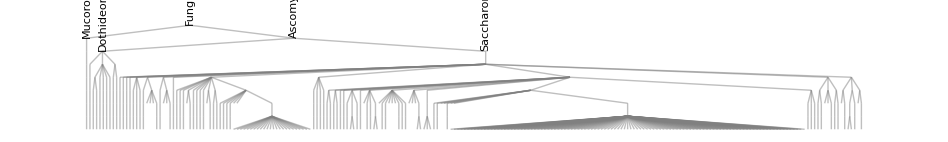

```mathematica
TreePlot[g, VertexRenderingFunction->(vfn[#2, #1]&), EdgeRenderingFunction->({Opacity[0.5], Gray,Line[#]}&), AspectRatio->0.15]
```